```mathematica
SetDirectory[NotebookDirectory[]];
Nc=3.;
mf2[h_,ρ_]:=(h^2 ρ)/2;
pF[μ_,h_,ρ_]:=√(μ^2-mf2[h,ρ]);
gamma[ps_,ρ_,h_,μ_,Mmass_,MZ_]:=(Nc h^2)/(8 π^2)(2 μ pF[μ,h,ρ]+mf2[h,ρ] Log[(μ-pF[μ,h,ρ])/(μ+pF[μ,h,ρ])]+1/2 ps^2((√(ps^2+4 mf2[h,ρ])-2 μ)/ps Log[Abs[(ps+2 pF[μ,h,ρ])/(ps-2pF[μ,h,ρ])]]-Log[(pF[μ,h,ρ]+μ)^2/mf2[h,ρ]]+(√(ps^2+4 mf2[h,ρ]))/ps Log[(2 mf2[h,ρ]+ps pF[μ,h,ρ]+μ √(ps^2+4 mf2[h,ρ]))/(2 mf2[h,ρ]-ps pF[μ,h,ρ]+μ √(ps^2+4 mf2[h,ρ]))]));
gammavac[ps_,ρ_,h_,Mmass_,MZ_]:=-(h^2 Nc)/(8 π^2)(mf2[h,ρ](1/2+Log[mf2[h,ρ]/Mmass^2])+1/2 ps^2(-2+Log[mf2[h,ρ]/MZ^2]+(√(ps^2+4 mf2[h,ρ]))/ps Log[(√(ps^2+4 mf2[h,ρ])+ps)/(√(ps^2+4 mf2[h,ρ])-ps)]));
gammavacp0[ρ_,h_,Mmass_,MZ_]:=Limit[-(h^2 Nc)/(8 π^2)(mf2[h,ρ](1/2+Log[mf2[h,ρ]/Mmass^2])+1/2 ps^2(-2+Log[mf2[h,ρ]/MZ^2]+(√(ps^2+4 mf2[h,ρ]))/ps Log[(√(ps^2+4 mf2[h,ρ])+ps)/(√(ps^2+4 mf2[h,ρ])-ps)])),ps->0];
gamma2[p0_,ps_,ρ_,ρ0_,h_,μ_,Mmass_,MZ_]:=ps^2+(λ300 ρ+ν300)+gamma[ps,ρ,h,μ,Mmass,MZ]+gammavac[ps,ρ,h,Mmass,MZ]-(gammavac[ps,ρ0,h,Mmass,MZ]-gammavacp0[ρ0,h,Mmass,MZ]);
λ300=75.8;
ν300=-482.^2;
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

## Finite mu

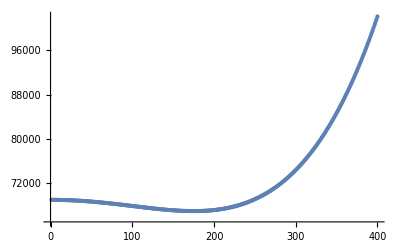

```mathematica
Table[gamma2[0.,N[i],fpi[[10]]^2/2,92.57845450044942^2/2,6.5,mu[[10]],300,300],{i,1,400,1}];
ListPlot[%]
```

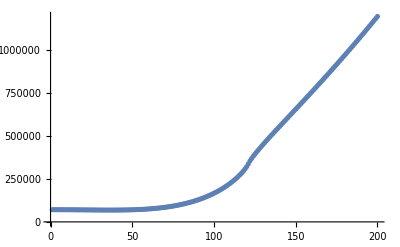

```mathematica
ListPlot[%]
```

```mathematica
fpi=Flatten[Import["./fpiT1.dat"]];
mu=Table[300+1*i,{i,1,150}];
Length[mu]
```

150

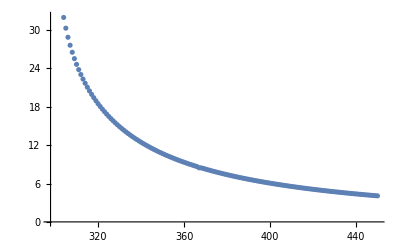

```mathematica
ListPlot[Transpose[{mu,fpi}]]
```

```mathematica
Emu=ParallelTable[FindMinimum[{gamma2[0.,ps,fpi[[j]]^2/2,92.57845450044942^2/2,6.5,mu[[j]],300,300]},{ps,108.8655359213690923641},WorkingPrecision->15,AccuracyGoal->12,PrecisionGoal->12][[2]][[1]][[2]]//Quiet,{j,1,150,1}]
```

{-1.58109015977458×10^-8,106.007061630396,122.020685270895,133.52037372985,142.769988386011,150.66970464188,157.654902133559,163.975699130008,169.791000576601,175.20553802864,180.298282505112,185.125456976164,189.724910217068,194.12954269572,198.366601879807,202.457473081942,206.418985321906,210.264815371795,214.007308072872,217.657095861489,221.219197992704,224.704774058229,228.11904557659,231.467983438035,234.756462832669,237.9878541498,241.16580997529,244.295481299895,247.378853230236,250.419576765346,253.41937380517,256.380713581556,259.30576088239,262.196414746875,265.054415855119,267.881366384686,270.678739713053,273.44793027015,276.190276209517,278.90675796751,281.598393413691,284.26650023448,286.912119918066,289.535678513515,292.137963879475,294.720144673972,297.283092062893,299.831452093311,302.352867499336,304.861210321045,307.352565219852,309.827261783832,312.286071587477,314.72968166406,317.158293396247,319.572228248454,321.972153833994,324.358528633588,326.731421618984,329.091338025156,331.438723548239,333.77399227557,336.097005336745,338.408497443959,340.708757674468,342.997891855112,345.303478977269,347.544004484684,349.801509751441,352.048971078527,354.286607910837,356.514646183424,358.733295564054,360.942762949592,363.143288465004,365.335030218871,367.51804140948,369.69277289194,371.859289408461,374.017570634669,376.167980297886,378.31064700412,380.445710347928,382.573267186989,384.693520210895,386.806743420667,388.912581739049,391.011702599462,393.103987940532,395.189695862544,397.268685487501,399.341318631061,401.407621071344,403.467675041222,405.521656504141,407.569683557129,409.611685381591,411.647941582576,413.678504709102,415.703413494792,417.722764674188,419.736721715556,421.745324037249,423.748646560629,425.746772503016,427.739797414432,429.727792378297,431.710833763111,433.688996146863,435.662350762604,437.630968861368,439.594934940459,441.554300801715,443.50909150637,445.459472992562,447.405464034228,449.34704338638,451.284363049305,453.217511723221,455.146463767306,457.071304491633,458.992106794079,460.908913751615,462.821765883816,464.730758022619,466.635909215059,468.537256615537,470.434865933332,472.329053234119,474.219076289905,476.105761134628,477.988918995856,479.868559316834,481.744729321694,483.617479943761,485.486883714685,487.352908602269,489.215664413313,491.075178455237,492.931466960279,494.784580092596,496.634557721835,498.481435211087,500.325249054712,502.166035211425,504.003828880177,505.838664627462,507.670578230781,509.499602885117,511.325760063862}

```mathematica
mf=Table[√mf2[6.5,fpi[[i]]^2/2],{i,1,150,1}]
```

{299.716,119.633,110.62,103.885,98.432,93.8034,89.7682,86.1864,82.9637,80.0382,77.3551,74.8755,72.5792,70.4434,68.4461,66.5706,64.8043,63.1373,61.5588,60.0587,58.6414,57.2887,55.999,54.7661,53.5858,52.458,51.3805,50.3433,49.3483,48.3889,47.4666,46.5784,45.722,44.8956,44.0977,43.3266,42.5811,41.8597,41.1606,40.4838,39.8289,39.1929,38.5743,37.975,37.3949,36.8303,36.2796,35.7128,35.2251,34.7182,34.2247,33.7457,33.2788,32.8218,32.3765,31.9434,31.5202,31.1058,30.7027,30.3094,29.9245,29.5469,29.1809,28.822,28.4698,28.1258,27.4921,27.4603,27.1379,26.8224,26.5133,26.2105,25.9139,25.6234,25.3381,25.0584,24.7857,24.5165,24.2518,23.9942,23.7408,23.4917,23.2471,23.0075,22.772,22.5383,22.3137,22.09,21.8708,21.6538,21.4432,21.2348,21.0301,20.8292,20.6311,20.4353,20.2448,20.0562,19.8703,19.688,19.5092,19.3322,19.1582,18.9869,18.8183,18.6523,18.4888,18.3277,18.1691,18.0128,17.8589,17.7069,17.5572,17.4106,17.2649,17.121,16.9807,16.8419,16.704,16.5688,16.4355,16.3039,16.174,16.0463,15.9196,15.7947,15.6718,15.5506,15.424,15.3127,15.1962,15.0805,14.9667,14.8548,14.7441,14.634,14.5267,14.42,14.3143,14.2103,14.1075,14.0059,13.9056,13.8065,13.7085,13.6117,13.5161,13.4216,13.3281,13.236}

```mathematica
pfermi=√(mu^2-mf^2)
```

{27.769,277.294,282.086,285.699,288.68,291.268,293.582,295.696,297.654,299.489,301.226,302.882,304.469,305.996,307.474,308.908,310.305,311.669,313.004,314.313,315.598,316.863,318.109,319.338,320.552,321.752,322.938,324.113,325.278,326.433,327.579,328.716,329.846,330.969,332.085,333.195,334.299,335.398,336.492,337.581,338.666,339.747,340.824,341.897,342.967,344.034,345.098,346.163,347.218,348.274,349.327,350.379,351.428,352.475,353.521,354.564,355.606,356.646,357.685,358.722,359.758,360.792,361.825,362.857,363.888,364.918,365.969,366.974,368.001,369.027,370.051,371.075,372.099,373.121,374.143,375.164,376.184,377.204,378.223,379.242,380.26,381.277,382.294,383.31,384.326,385.341,386.356,387.371,388.385,389.398,390.412,391.424,392.437,393.449,394.461,395.472,396.483,397.494,398.505,399.515,400.525,401.535,402.544,403.554,404.563,405.571,406.58,407.588,408.596,409.604,410.612,411.619,412.627,413.634,414.641,415.648,416.654,417.661,418.667,419.673,420.679,421.685,422.691,423.696,424.702,425.707,426.712,427.717,428.723,429.727,430.732,431.737,432.741,433.746,434.75,435.754,436.758,437.763,438.767,439.77,440.774,441.778,442.782,443.785,444.789,445.792,446.796,447.799,448.802,449.805}

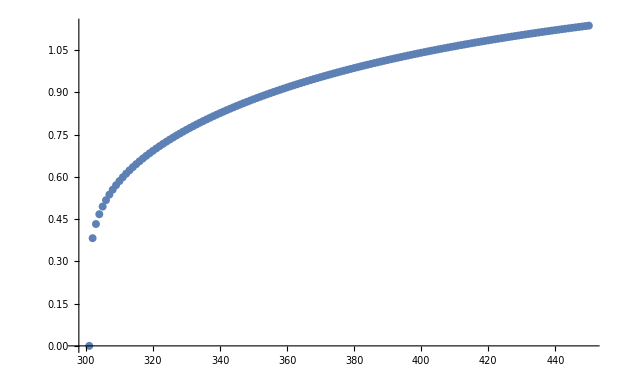

```mathematica
ListPlot[Transpose[{mu,Emu/pfermi}],PlotRange->All]
```

```mathematica
Export["pFT0.dat",pfermi]
Export["pminT0.dat",Emu]
```

pFT0.dat

pminT0.dat

```mathematica
Export["T1.dat",T1]
```

T1.dat

```mathematica
ET1=Table[ParallelTable[gamma2[0.,ps,fpi[[j]]^2/2,6.5,T[[j]],320.,300.,300.]+(0.)^2+(ps)^2+(λ300 fpi[[j]]^2/2+ν300),{ps,280.,360.,2}],{j,1,1,1}];
```

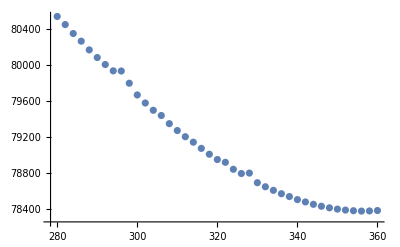

```mathematica
ListPlot[Transpose[{Flatten[Table[i,{i,280,360,2}]],Flatten[ET1]}]]
```